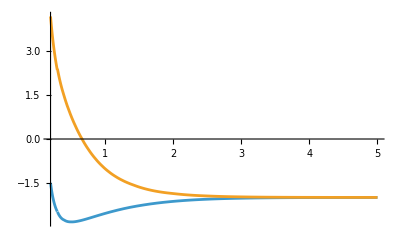

```mathematica
geradeData=Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1sV3.mx"];
geradePotential=Table[{geradeData⟦i,1⟧,geradeData⟦i,3⟧},{i,1,27}];

ungeradeData=Import["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1sV3.mx"];
ungeradePotential=Table[{ungeradeData⟦i,1⟧,ungeradeData⟦i,3⟧},{i,1,27}];
long[R_]:=-2.0-0.082/R^4;
geradefun=Interpolation[geradePotential];
ungeradefun=Interpolation[ungeradePotential];

(*Fit to a model*)
gdata=Drop[geradePotential,{5,27}];
udata=Drop[ungeradePotential,{5,27}];
model[R_,C1_,C2_,C3_]:=C1 Exp[-C2 R]/R+C3;

gnlm=NonlinearModelFit[gdata,model[R,C1,C2,C3],{C1,C2,C3},R];
unlm=NonlinearModelFit[udata,model[R,C1,C2,C3],{C1,C2,C3},R];
gshort[R_]:=model[R,C1,C2,C3]/. gnlm["BestFitParameters"];
ushort[R_]:=model[R,C1,C2,C3]/. unlm["BestFitParameters"];
gpot[R_]=Piecewise[{{gshort[R],R≤0.3},{geradefun[R],0.3<R<13.0},{long[R],R≥13.0}}];
upot[R_]=Piecewise[{{ushort[R],R≤0.3},{ungeradefun[R],0.3<R<13.0},{long[R],R≥13.0}}];
Plot[{gpot[R],upot[R]},{R,0.2,5},PlotRange->All]
```

```mathematica
(*e=0.1/27.21;*)
μ=1866.0/2.0;
(*k=2 μ e;*)
kB=0.695; (*Boltzman in AU,cm-1K*)
(*λ=2π/k*)
a0=5.29188^-11;
r0=0.01;
rend=100;

(* For a single partial wave m, energy e and distance r, up to rend*)
computePhaseShifts[m_,e_,r0_,rend_] := Module[{k,equG,equU,solsG,solsU,fg,fu, ylogG, ylogU, sl, cl, slp, clp, bG, bU},
k=√(2 μ e);
equG:=yg''[r]+yg'[r]/r-2 μ (gpot[r]+2) yg[r]-m^2/r^2 yg[r]+2 μ e yg[r];
equU:=yu''[r]+yu'[r]/r-2 μ (upot[r]+2) yu[r]-m^2/r^2 yu[r]+2 μ e yu[r];
solsG=Flatten[NDSolve[{equG==0,yg[r0]==0,yg'[r0]==1},yg,{r,r0,rend},MaxSteps->200000]];
solsU=Flatten[NDSolve[{equU==0,yu[r0]==0,yu'[r0]==1},yu,{r,r0,rend},MaxSteps->200000]];
fg[r_]=yg[r]/. solsG;
fu[r_]=yu[r]/. solsU;
If[(e>0.002&&e<0.004)&&(m==40||m==5||m==0),Print["k=",k];
Print[Plot[fg[r],{r,r0,rend},PlotLabel->StringJoin["m=",ToString[m],", e=",ToString[e],"eV"],AxesLabel->"R"]]];
ylogG[r_]:=fg'[r]/fg[r];
ylogU[r_]:=fu'[r]/fu[r];
sl[n_,r_]:=BesselJ[n,k r];
cl[n_,r_]:=HankelH1[n,k r];
slp[n_,r_]:=Derivative[0,1][sl][n,r];
clp[n_,r_]:=Derivative[0,1][cl][n,r];
bG[n_,r_]:=(-I)^(Abs[n]) (slp[n,r]-ylogG[r]×sl[n,r])/(clp[n,r]-ylogG[r]×cl[n,r]);
bU[n_,r_]:=(-I)^(Abs[n]) (slp[n,r]-ylogU[r]×sl[n,r])/(clp[n,r]-ylogU[r]×cl[n,r]);
If[m==0,Return[{Abs[N[bG[m,rend]]],Abs[N[bG[m,rend]-bU[m,rend]]]^2}],
Return[{2 Abs[N[bG[m,rend]]],2 Abs[N[bG[m,rend]-bU[m,rend]]]^2}]]	
];
(*computePhaseShifts[10,0.003,0.1,100]*)
```

k=2.02846

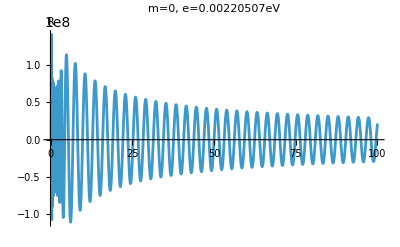

k=2.02846

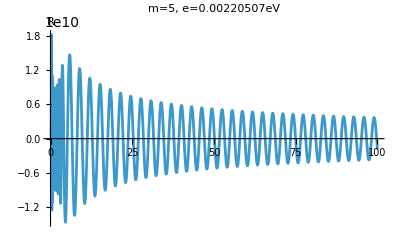

k=2.02846

-Graphics-

k=2.19099

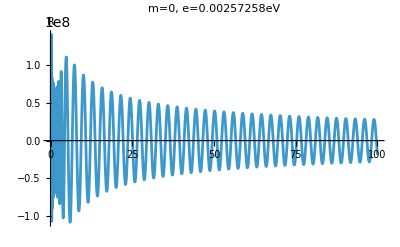

k=2.19099

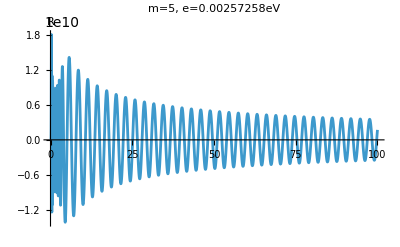

k=2.19099

-Graphics-

k=2.34227

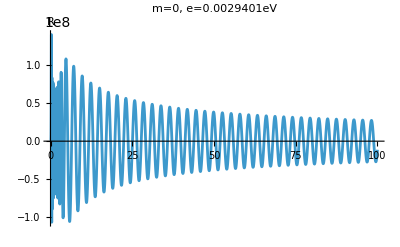

k=2.34227

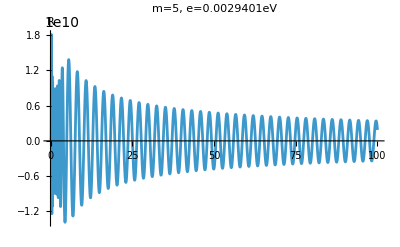

k=2.34227

-Graphics-

k=2.48435

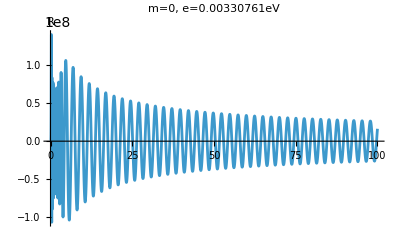

k=2.48435

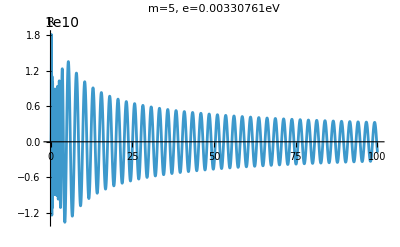

k=2.48435

-Graphics-

k=2.61873

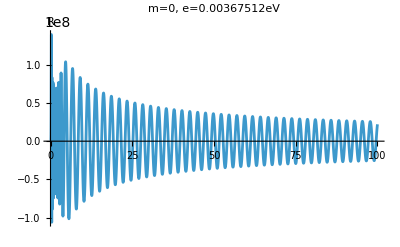

k=2.61873

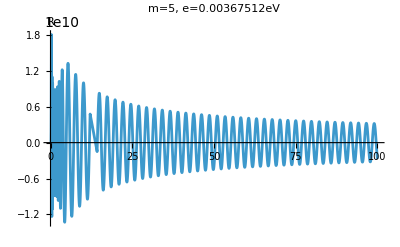

k=2.61873

-Graphics-

InterpolatingFunction[…]

```mathematica
(*e=collision energy in eV,r0,rend-R range*)
computeCrossSect[eV_,r0_,rend_]:=Module[{phaseShiftForAllm,eH,kk,crossSection},
eH=eV/27.21; (*energy Hartree*)
kk=2 μ eH;
(*m-partial waves*)
phaseShiftForAllm=Table[{m,computePhaseShifts[m,eH,r0,rend]},{m,0,40}];
crossSection=Total[phaseShiftForAllm,{1}][[2]];
{eV, crossSection}
];


crossSection=Table[computeCrossSect[e,r0,rend],{e,0.01,1,0.01}];
crossSectionGraphSC=Interpolation[{crossSection⟦All,1⟧,crossSection⟦All,2⟧⟦All,1⟧}//Transpose]
crossSectionGraphCT=Interpolation[{crossSection⟦All,1⟧,crossSection⟦All,2⟧⟦All,2⟧}//Transpose];
```

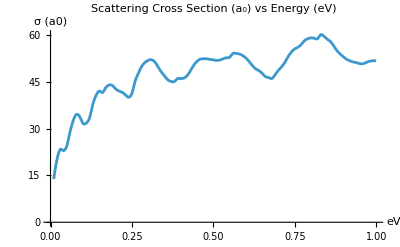

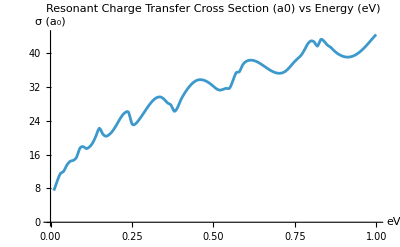

```mathematica
Plot[crossSectionGraphSC[e],{e,0.01,1},AxesOrigin->{0,0},AxesLabel->{"eV","σ (a0)"},PlotLabel->"Scattering Cross Section (a_0) vs Energy (eV)"]
Plot[crossSectionGraphCT[e],{e,0.01,1},AxesOrigin->{0,0},AxesLabel->{"eV","σ (a_0)"},PlotLabel->"Resonant Charge Transfer Cross Section (a0) vs Energy (eV)"]
```